```mathematica
ClearAll[R, alpha];
alpha = 1.5;
```

```mathematica
R[1] := 0;
R[n_Integer?Positive] := R[n] = 1 + Min[Table[(R[k] + R[n - k])/alpha, {k, 1, n - 1}]];
```

```mathematica
rTable = Table[{n, R[n]}, {n, 1, 100}];
```

```mathematica
ListLinePlot[
  rTable,
  PlotStyle -> Black,
  PlotMarkers -> Automatic,
  AxesLabel -> {"n", "R(n)"},
  PlotLabel -> "Recursive Depth Function R(n)",
  Epilog -> {
    {Red, Dashed, 
     Line[{{1, alpha/(alpha - 1)}, {100, alpha/(alpha - 1)}}]}
  },
  ImageSize -> Large
]
```

-Graphics-

```mathematica
Grid[Partition[rTable[[1 ;; 20]], 5], Frame -> All]
```

{1,0} | {2,1.} | {3,1.66667} | {4,2.11111} | {5,2.40741}
{6,2.60494} | {7,2.73663} | {8,2.82442} | {9,2.88294} | {10,2.92196}
{11,2.94798} | {12,2.96532} | {13,2.97688} | {14,2.98459} | {15,2.98972}
{16,2.99315} | {17,2.99543} | {18,2.99696} | {19,2.99797} | {20,2.99865}

```mathematica
ClearAll[recursiveZeta];
recursiveZeta[s_] := N[Sum[Exp[-R[n]] / n^s, {n, 1, 100}]];
```

```mathematica
Print["Recursive Zeta Transform at s = 2: ", recursiveZeta[2]];
```

Recursive Zeta Transform at s = 2: 1.13395

```mathematica
ClearAll[getSplits, recursiveTreePlot];
```

```mathematica
getSplits[1] := {};
getSplits[n_Integer?Positive] := Module[{minK},
  minK = First@MinimalBy[
    Table[{k, (R[k] + R[n - k])/alpha}, {k, 1, n - 1}],
    Last
  ][[1]];
  Join[{{n -> minK, n -> (n - minK)}}, getSplits[minK], getSplits[n - minK]]
];
```

```mathematica
recursiveTreePlot[n_Integer?Positive] := Module[{edges},
  edges = getSplits[n];
  GraphPlot[
    edges,
    VertexLabels -> "Name",
    DirectedEdges -> True,
    PlotLabel -> Row[{"Optimal Recursive Division Tree for R(", n, ")"}],
    ImageSize -> Medium
  ]
];
```

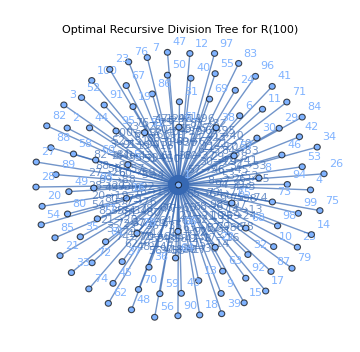

```mathematica
recursiveTreePlot[100]
```